## Cálculo de parámetros en una economía de mercado

```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
Q=L^β k^(1-β); (*Función de producción de la firma*)
R=V/Q^η; (*Oferta-demanda agregada: Q es la cantidad de productos que la gente compraría a un precio R*)
F=R Q-L W-r k//Simplify;(*Ganancia que obtiene una firma. k es el capital que pide prestado a un agente, r el interés, L la cantidad de trabajadores, W el salario que la firma paga a cada trabajador, Q el número de artículos de un producto y Q el número de agentes a quienes vende dichos productos*)
```

```mathematica
nablaF=Grad[F,{L,k}]
```

{-W+((k^(1-β) L^β)^(1-η) V β (1-η))/L,-r+((k^(1-β) L^β)^(1-η) V (1-β) (1-η))/k}

```mathematica
(L nablaF[[1]]==0)//Simplify 
(k nablaF[[2]]==0)//Simplify
```

L W+(k^(1-β) L^β)^(1-η) V β (-1+η)==0

k r==(k^(1-β) L^β)^(1-η) V (-1+β) (-1+η)

```mathematica
eq1=(L W==(k^(1-β) L^β)^(1-η) V β (1-η))(*Ecuaciones a resolver para maximizar la ganancia de la firma*)
eq2=(k r==(k^(1-β) L^β)^(1-η) V (1-β) (1-η))
```

L W==(k^(1-β) L^β)^(1-η) V β (1-η)

k r==(k^(1-β) L^β)^(1-η) V (1-β) (1-η)

```mathematica
eq3=(eq2[[1]]/eq1[[1]]==eq2[[2]]/eq1[[2]])(*obtememos una ecuación más sencilla que relacione a L crítico con K crítico*)
```

(k r)/(L W)==(1-β)/β

```mathematica
krule=Solve[eq3,k][[1,1]](*Resolvemos para K crítico*)
```

k→-(L W (-1+β))/(r β)

```mathematica
eq1/.krule (*Eliminamos a K en una de las ecuaciones*)
```

L W==V (L^β (-(L W (-1+β))/(r β))^(1-β))^(1-η) β (1-η)

```mathematica
eq4=(W==V L^-η((W (1-β))/(r β))^((1-β)(1-η)) β (1-η))(*Simplificamos a mano la ec anterior para tener un solo término con L*)
```

W==L^-η V ((W (1-β))/(r β))^((1-β) (1-η)) β (1-η)

```mathematica
Lrule=Solve[eq4,L][[1,1]]//Simplify(*Resolvemos L crítico*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

L→((V (-1+β) ((W-W β)/(r β))^(β (-1+η)-η) (-1+η))/r)^(1/η)

```mathematica
krule=krule/.Lrule(*Resolvemos K crítico*)
```

k→-(W (-1+β) ((V (-1+β) ((W-W β)/(r β))^(β (-1+η)-η) (-1+η))/r)^(1/η))/(r β)

```mathematica
parameters={V->100,η->1/2,β->8/10,W->10,r->0.15};
TableForm[(TableForm[{{"L = ",Floor[L], "trabajadores"},{"K = ",k, "$"},{"Q = ",Floor[Q], "artículos"},{"R = ",R, "$ (precio de artículo)"},{"F = ",F, "$ (Ganancia)"}}]/.{Lrule,krule})/.parameters]
(*Por último asignamos valores a los parámetros y obtenemos la ganancia máxima*)
```

L =  | 28 | trabajadores
K =  | 468.1 | $
Q =  | 49 | artículos
R =  | 14.242 | $ (precio de artículo)
F =  | 351.075 | $ (Ganancia)

```mathematica
parameters={V->100,η->1/2,β->8/10,W->10};
kFunction=k/.krule/.parameters;
```

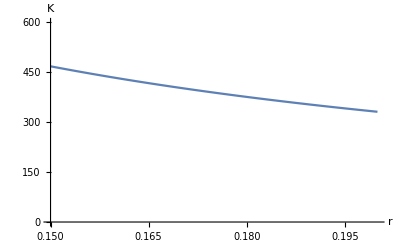

```mathematica
Plot[kFunction,{r,0.15,0.20},
PlotRange->{0,600},AxesLabel->{"r","K"}]
```

```mathematica
kFunction/.r->0.20
```

331.445

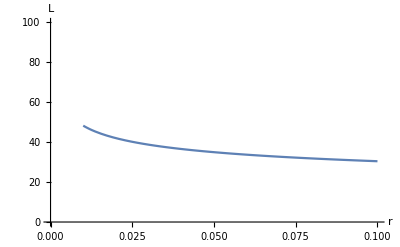

```mathematica
parameters={V->100,η->1/2,β->8/10,W->10};
LFunction = L/.Lrule/.parameters;
Plot[LFunction,{r,0.01,0.10},
PlotRange->{0,100},AxesLabel->{"r","L"}]
```

```mathematica
BGdist = 1/T Exp[-m/T];
```

```mathematica
Integrate[BGdist,{m,T,Infinity},Assumptions->T>0]
```

1/ⅇ

```mathematica
N[%]
```

0.367879